# Kalman Folding

Brian Beckman

17 April 2016

## Preliminaries

```mathematica
<<"Notation`"
InfixNotation[⊕,Join];
```

```mathematica
ClearAll[col,row,id,con,zero,len,dim,m,f1,inv,pinv,scalar,groundTruth];
col[xs_List]:=List/@xs;
row[xs_List]:=List[xs];
id=IdentityMatrix;
con[c_,m_,n_]:=ConstantArray[c,{m,n}];
con[c_,n_]:=con[c,n,n];
zero[m_,n_]:=con[0,m,n];
zero[n_]:=con[0,n];
len=Length;
dim[squareMatrix_List]:=len[squareMatrix⟦1⟧];
m=MatrixForm;
f1=Flatten[#,1]&;
inv=Inverse;
pinv=PseudoInverse;
scalar[m1x1_]:=m1x1⟦1,1⟧;
groundTruth=({{-3}, {9}, {-4}, {-5}});
```

## Time-Independent Model

Unit observation covariance, Generalized below in the time-dependent model.

```mathematica
ClearAll[kalman];
kalman[{x_,P_},{A_,z_}]:=
Module[{D,K},
D=id[len[z]]+A.P.Transpose[A];
K=P.Aᵀ.inv[D];
{x+K.(z-A.x),P-K.D.Transpose[K]}];
```

```mathematica
ClearAll[testCase];
m/@(testCase={
{{{1,0.,0.,0.}},{-2.28442}},
{{{1,1.,1.,1.}},{-4.83168}},
{{{1,-1.,1.,-1.}},{-10.4601}},
{{{1,-2.,4.,-8.}},{1.40488}},
{{{1,2.,4.,8.}},{-40.8079}}})
```

{({1,0.,0.,0.}
-2.28442),({1,1.,1.,1.}
-4.83168),({1,-1.,1.,-1.}
-10.4601),({1,-2.,4.,-8.}
1.40488),({1,2.,4.,8.}
-40.8079)}

```mathematica
m@(m/@#&/@
Chop[FoldList[
kalman,
{col[{0,0,0,0}],
id[4]*1000.0},
testCase
]])
```

((0
0
0
0) | (1000. | 0 | 0 | 0
0 | 1000. | 0 | 0
0 | 0 | 1000. | 0
0 | 0 | 0 | 1000.)
(-2.28214
0
0
0) | (0.999001 | 0 | 0 | 0
0 | 1000. | 0 | 0
0 | 0 | 1000. | 0
0 | 0 | 0 | 1000.)
(-2.28299
-0.849281
-0.849281
-0.849281) | (0.998669 | -0.332779 | -0.332779 | -0.332779
-0.332779 | 666.889 | -333.111 | -333.111
-0.332779 | -333.111 | 666.889 | -333.111
-0.332779 | -333.111 | -333.111 | 666.889)
(-2.28749
1.40675
-5.35572
1.40675) | (0.998004 | 0 | -0.997506 | 0
0 | 500.125 | 0 | -499.875
-0.997506 | 0 | 1.49676 | 0
0 | -499.875 | 0 | 500.125)
(-2.29399
7.92347
-5.34488
-5.1154) | (0.997508 | 0.49762 | -0.996678 | -0.498035
0.49762 | 1.3855 | -0.829836 | -0.719881
-0.996678 | -0.829836 | 1.49538 | 0.830528
-0.498035 | -0.719881 | 0.830528 | 0.553787)
(-2.97423
7.2624
-4.21051
-4.45378) | (0.485458 | 0 | -0.142778 | 0
0 | 0.901908 | 0 | -0.235882
-0.142778 | 0 | 0.0714031 | 0
0 | -0.235882 | 0 | 0.0693839))

Insensitivity to A-Priori Observation Covariance

```mathematica
m/@Chop[Fold[kalman,{col[{0,0,0,0}],id[4]*1000.0},testCase]]
```

{(-2.97423
7.2624
-4.21051
-4.45378),(0.485458 | 0 | -0.142778 | 0
0 | 0.901908 | 0 | -0.235882
-0.142778 | 0 | 0.0714031 | 0
0 | -0.235882 | 0 | 0.0693839)}

```mathematica
m/@Chop[Fold[kalman,{col[{0,0,0,0}],id[4]*1000000.0},testCase]]
```

{(-2.97507
7.27
-4.21039
-4.4558),(0.485714 | 0 | -0.142857 | 0
0 | 0.902777 | 0 | -0.236111
-0.142857 | 1.05409×10^-10 | 0.0714285 | 0
0 | -0.236111 | 0 | 0.0694444)}

## Time-Dependent Filter

Process-Noise Matrix

Process noise always enters the last state, and with a constant standard deviation. We must integrate the process-noise covariance matrix over a discrete time interval and a particular model of system dynamics to add its effects to the filter.

```mathematica
ClearAll[Q,Φ,σx,t];
Q=({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}});
Φ[t_]:=({{1, t, t^2/2}, {0, 1, t}, {0, 0, 1}});
Integrate[Φ[t].Q.Transpose[Φ[t]],{t,0,dt}]//m
```

(dt^5/20 | dt^4/8 | dt^3/6
dt^4/8 | dt^3/3 | dt^2/2
dt^3/6 | dt^2/2 | dt)

As A Fold

gen is a way to generate random samples from a covariance matrix. This only honors the diagonal terms, but each diagonal term individually.

kalman is the Kalman filter with time-dependent dynamical process (also called state estimation).

At the bottom, we validate that kalman degenerates to the original static case (also called parameter estimation).

Ξ is the integrated process-noise matrix. It depend on time and on the size of the time step.

Φ is the integral of the system-dynamics matrix F; more precisely, it is Exp[F t].

Γ is time-step integral of system response G propagated by Φ.

Ξ, Φ, Γ, and u may all depend on time and on the size of the time step.

```mathematica
ClearAll[gen,kalman];
(* generate noisy fake observations *)
gen[P_]:=
Module[{σs},
σs=Sqrt/@Table[P[[i,i]],{i,dim[P]}];
If[Chop[#]==0,0,(* RandomVariate can't handle a zero σ *)
RandomVariate[NormalDistribution[0.0,#]]]&/@σs];
(* this is a function-maker -- give it an obs noise covar and get a foldable function *)
kalman[Ζ_][{x_,P_},{Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K},
x2=Φ.x+Γ.u;
P2=Ξ+Φ.P.Transpose[Φ];
(* below this line is just like the time-independent model! *)
D=Ζ+A.P2.Transpose[A];
K=P2.Transpose[A].inv[D];
{x2+K.(z-A.x2),P2-K.D.Transpose[K]}];
(* show that it degenerates to the time-independent case *)
m/@
Chop[
With[{
Ξ=zero[4],Ζ=id[1],
Φ=id[4],Γ=zero[4,1],u=zero[1]},
Fold[
kalman[Ζ],
{col[{0,0,0,0}],
id[4]*1000.0},
{Ξ,Φ,Γ,u}⊕#&/@testCase
]]]
```

{(-2.97423
7.2624
-4.21051
-4.45378),(0.485458 | 0 | -0.142778 | 0
0 | 0.901908 | 0 | -0.235882
-0.142778 | 0 | 0.0714031 | 0
0 | -0.235882 | 0 | 0.0693839)}

Track a Falling Object

Repro an example from Zarchan and Musoff, Fundamentals of Kalman Filtering, A Practical Approach, Ch. 4, track a falling object, no air drag. There are three states: the position x, velocity ẋ, acceleration ẍ ; and the observations z directly measure the position state.

State-space dynamics:

```mathematica
ClearAll[x,xd,xdd,Ψ,g,u,F,Φ,Ξc,Ξ,G,Γ,A];
g=-32.2;
u[t_]:=col[{g}];
Ψ=({{x}, {xd}, {xdd}});F=({{0, 1, 0}, {0, 0, 1}, {0, 0, 0}});G=({{0}, {0}, {1}});
Φ[dt_]:=({{1, dt, dt^2/2}, {0, 1, dt}, {0, 0, 1}});Γ[dt_]:=({{dt^2/2}, {dt}, {1}});
Ξc=({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}});
Ξ[dt_]:=({{dt^5/20, dt^4/8, dt^3/6}, {dt^4/8, dt^3/3, dt^2/2}, {dt^3/3, dt^2/2, dt}});
A[t_]:=({{1, 0, 0}});
```

```mathematica
ClearAll[experiment,withTimes,myStyle];
withTimes[times_,obj_]:=MapThread[List,{times,obj}];
myStyle[s_String]:=Style[s,FontFamily->"Candara",FontSize->12];

experiment[
startTime_,
endTime_,
timeIncrement_,
aPrioriState_,
aPrioriCovariance_,
fakeFn_,
trueObservationFn_,
trueObservationDerivativeFn_]:=
Module[{t,timesIter,times,fakes,ests},
timesIter={t,startTime,endTime,timeIncrement};
times=Table[t,Evaluate@timesIter];
fakes=Table[fakeFn[timeIncrement,t],Evaluate@timesIter];
ests=FoldList[kalman[Ζ],{aPrioriState,aPrioriCovariance},fakes];
Grid@{{ListLinePlot[{
withTimes[times,
Table[trueObservationFn[t],Evaluate@timesIter]-
ests⟦;;,1,1,1⟧]},
Frame->True,
FrameLabel->{{
myStyle@"Position Residual / foot",""},{
myStyle@"time / sec",
myStyle@"Position Residuals vs. Time"}},
GridLines->Automatic,
ImageSize->Medium],
ListLinePlot[{
withTimes[times,
Table[trueObservationDerivativeFn[t],Evaluate@timesIter]-
ests⟦2;;,1,2,1⟧]},
Frame->True,
FrameLabel->{{
myStyle@"Speed Residual / [foot/sec]",""},{
myStyle@"time / sec",
myStyle@"Speed Residuals vs. Time"}},
GridLines->Automatic,
ImageSize->Medium]}
{ListLinePlot[{
withTimes[times,Table[trueObservationFn[t],Evaluate@timesIter]],
withTimes[times,ests⟦2;;,1,1,1⟧]},
Frame->True,
FrameLabel->{{
myStyle@"Position / foot",""},{
myStyle@"time / sec",
myStyle@"Position Truth and Estimate vs. Time"}},
GridLines->Automatic,
ImageSize->Medium],
ListLinePlot[{
withTimes[times,Table[trueObservationDerivativeFn[t],Evaluate@timesIter]],
withTimes[times,ests⟦2;;,1,2,1⟧]},
Frame->True,
FrameLabel->{{
myStyle@"Speed / [foot/sec]",""},{
myStyle@"time / sec",
myStyle@"Speed Truth and Estimate.7f vs. Time"}},
GridLines->Automatic,
ImageSize->Medium]}}];
```

```mathematica
ClearAll[experiment,withTimes,myStyle];
withTimes[times_,obj_]:=MapThread[List,{times,obj}];
myStyle[s_String]:=Style[s,FontFamily->"Candara",FontSize->12];

experiment[
startTime_,
endTime_,
timeIncrement_,
aPrioriState_,
aPrioriCovariance_,
fakeFn_,
trueObservationFn_,
trueObservationDerivativeFn_]:=
Module[{t,timesIter,times,fakes,ests},
timesIter={t,startTime,endTime,timeIncrement};
times=Table[t,Evaluate@timesIter];
fakes=Table[fakeFn[timeIncrement,t],Evaluate@timesIter];
ests=FoldList[kalman[Ζ],{aPrioriState,aPrioriCovariance},fakes];
Grid@{{ListLinePlot[{
withTimes[times,
Table[trueObservationFn[t],Evaluate@timesIter]-ests⟦2;;,1,1,1⟧],
withTimes[times,Sqrt@ests⟦2;;,2,1,1⟧],
withTimes[times,-Sqrt@ests⟦2;;,2,1,1⟧]},
Frame->True,
FrameLabel->{{
myStyle@"Position Residual / foot",""},{
myStyle@"time / sec",
myStyle@"Position Residuals vs. Time"}},
GridLines->Automatic,
ImageSize->Medium],
ListLinePlot[{
withTimes[times,
Table[trueObservationDerivativeFn[t],Evaluate@timesIter]-ests⟦2;;,1,2,1⟧],
withTimes[times,Sqrt@ests⟦2;;,2,2,2⟧],
withTimes[times,-Sqrt@ests⟦2;;,2,2,2⟧]},
Frame->True,
FrameLabel->{{
myStyle@"Speed Residual / [foot/sec]",""},{
myStyle@"time / sec",
myStyle@"Speed Residuals vs. Time"}},
GridLines->Automatic,
ImageSize->Medium]},
{ListLinePlot[{
withTimes[times,Table[trueObservationFn[t],Evaluate@timesIter]],
withTimes[times,ests⟦2;;,1,1,1⟧]},
Frame->True,
FrameLabel->{{
myStyle@"Position / foot",""},{
myStyle@"time / sec",
myStyle@"Position Truth and Estimates vs. Time"}},
GridLines->Automatic,
ImageSize->Medium],
ListLinePlot[{
withTimes[times,Table[trueObservationDerivativeFn[t],Evaluate@timesIter]],
withTimes[times,ests⟦2;;,1,2,1⟧]},
Frame->True,
FrameLabel->{{
myStyle@"Speed / [foot/sec]",""},{
myStyle@"time / sec",
myStyle@"Speed Truth and Estimate.7fs vs. Time"}},
GridLines->Automatic,
ImageSize->Medium]}}];
```

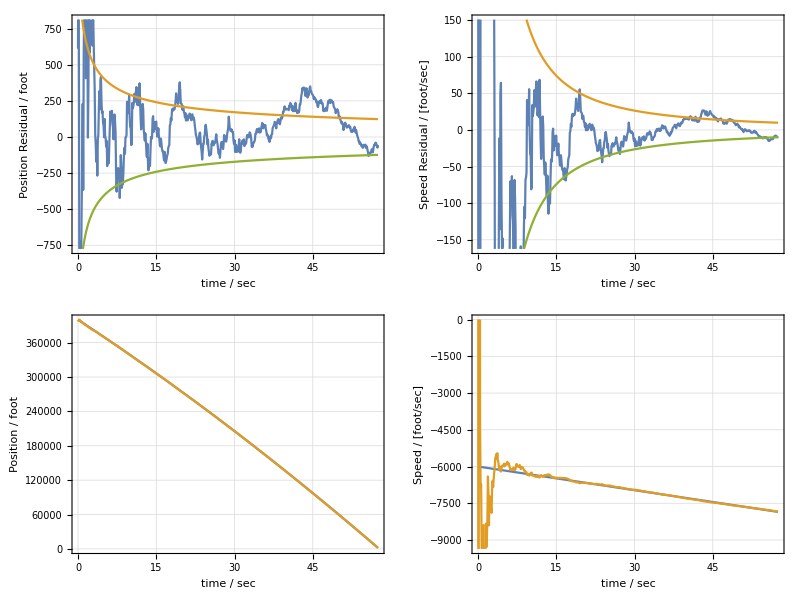

```mathematica
With[{x0=400000,v0=-6000,a0=-32.2},
With[{
aPrioriState=zero[3,1](*col[{x0,v0,a0}]*),
aPrioriCovariance=1000000000000000id[3],
Ζ=col[{1000.0^2}]},
experiment[
0,57.5,0.1,
aPrioriState,aPrioriCovariance,
{dt,t}↦
{0*({{dt^5/20, dt^4/8, dt^3/6}, {dt^4/8, dt^3/3, dt^2/2}, {dt^3/3, dt^2/2, dt}}),
({{1, dt, dt^2/2}, {0, 1, dt}, {0, 0, 1}}),
({{dt^2/2}, {dt}, {1}}),
zero[1],
({{1, 0, 0}}),
col[{x0+v0 t+(a0 t^2)/2}]+gen[Ζ]},
t↦x0+v0 t+a0 t^2/2,
t↦v0+a0 t
]]]
```

Doesn’t work well for a two-state system, but we can fix this.

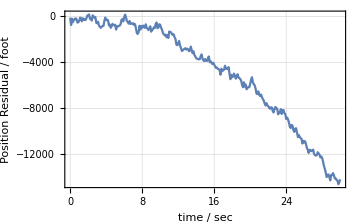
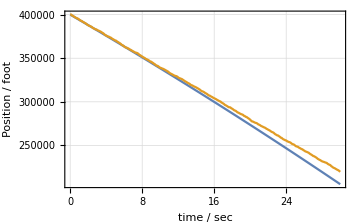
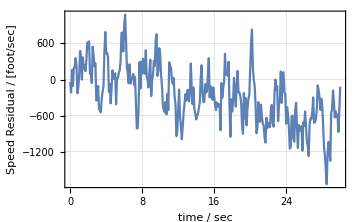
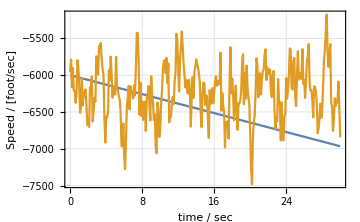
-Graphics- -Graphics- | -Graphics- -Graphics-

```mathematica
With[{x0=400000,v0=-6000,a0=-32.2,Ζ=col[{1000.0^2}]},
experiment[
0,30.,0.1,
col[{x0,v0}],
1000000id[2],
{dt,t}↦
{1000000*({{dt^3/3, dt^2/2}, {dt^2/2, dt}}),
({{1, dt}, {0, 1}}),
({{dt}, {1}}),
col[{g}],
({{1, 0}}),
col[{x0+v0 t}]+gen[Ζ]},
t↦x0+v0 t+a0 t^2/2,
t↦v0+a0 t]]
```